## Calculations for internal (and zero) dynamics & feedback linearization (Problem 11.8)

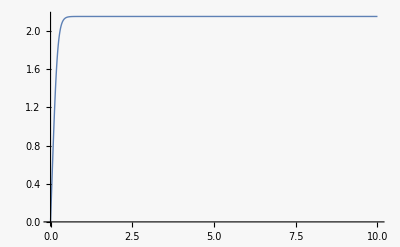

```mathematica
Clear["Global`*"];
tend=10;
ysol=NDSolveValue[{y'[t]==-y[t]^3+10,y[0]==0},y,{t,0,tend}];
Plot[ysol[t],{t,0,tend},PlotRange->All]
```

```mathematica
DSolve[{y'[t]==-y[t]^3,y[0]==y0},y[t],t]
```

{{y[t]→-1/(√(2 t+1/y0^2))},{y[t]→1/(√(2 t+1/y0^2))}}

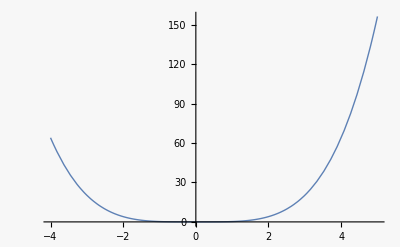

```mathematica
V=x^4/4+α x^3+(3 α^2)/2 x^2;
Plot[V/.α->0,{x,-4,5}]
```

```mathematica
Solve[D[V,x]==0,x]//FullSimplify
```

{{x→0},{x→-1/2 ⅈ (-3 ⅈ+√3) α},{x→1/2 ⅈ (3 ⅈ+√3) α}}

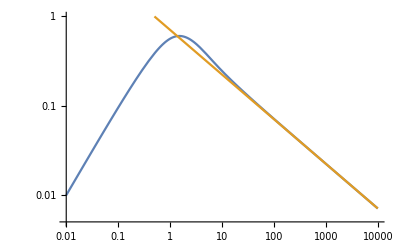

```mathematica
ysol1=NDSolveValue[{y'[t]==-y[t]^3+ⅇ^-t,y[0]==0},y,{t,0.01,10000}];
LogLogPlot[{Abs[ysol1[t]],1/(√(2 t))},{t,0.01,10000},PlotRange->{0.005,1}]
```

Export data

```mathematica
tval=Table[10^t,{t,-2,4,0.01}];
ysol1t=Table[ysol1[10^t],{t,-2,4,0.01}];
 (* 
 SetDirectory[NotebookDirectory[];
Export["internalDynamics.dat",Flatten/@Transpose[{tval,ysol1t}],"Table"] 
*)
```

```mathematica
DSolve[{y'[t]==+y[t]^3,y[0]==y0},y[t],t]//FullSimplify
```

{{y[t]→-1/(√(-2 t+1/y0^2))},{y[t]→1/(√(-2 t+1/y0^2))}}

Look at feedback linearization

```mathematica
sys=AffineStateSpaceModel[{{Subscript[x, 2]^3,0},{{1},{1}},{Subscript[x, 1]}},{Subscript[x, 1],Subscript[x, 2]}]
```

x_2^3011x_10x_1x_2211111NoneFalseFalseFalseFalseAutomaticAutomatic

```mathematica
ℱ=FeedbackLinearize[sys,{{Subscript[z, 1],Subscript[z, 2]},{v}}]
```

LinearizingTransformationData[Control`fb$1197370]

```mathematica
flin=ℱ["LinearSystem"]
```

0110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{z_1},{v}

```mathematica
k=StateFeedbackGains[flin,{-1}]
```

{{1}}

```mathematica
ℱ[{"ClosedLoopSystem",k}]
```

u_1-x_1u_1-x_1-x_2^3x_1x_1x_22111NoneNoneFalseFalseFalse{u_1}Automatic

```mathematica
ℱ["FeedbackCompensator"]
```

v-x_2^3u_10111NoneNoneFalseFalseFalse{v}Automatic

```mathematica
ℱ["InverseFeedbackCompensator"]
```

u_1+x_2^3v0111NoneNoneFalseFalseFalse{u_1}Automatic

```mathematica
ℱ["InverseFeedbackTransformation"]
```

{v→u_1+x_2^3}

```mathematica
ℱ["DecouplingMatrix"]
```

{{1}}

```mathematica
ℱ["PreCompensator"]
```

1StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1101FalseFalseFalseAutomaticNone,{},{u_1},{u_1}

```mathematica
ℱ["PostCompensator"]
```

1StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1101FalseFalseFalseAutomaticNone,{},{y_1}

```mathematica
ℱ["ZeroDynamicsSystem"]
```

-z_2^3z_2z_21011NoneNoneFalseFalseFalse{}Automatic

```mathematica
ℱ["ZeroDynamicsManifold"]
```

{x_1==0}